# MMA Notes

2023.09.04

# Everything is an expression

In Mathematica, everything is an expression. 
Every expression is a combination of normal expressions. 
A normal expression can be constructed using 3 parts: 1. atoms (symbol, number, string),  2. square brackets [],  3. commas , . 
The [] and commas can be regarded as the special symbols.

In summary, in MMA, everything is an expression, and every  expression is a combination of symbols.

### atoms

symbol

The Symbol in MMA, is a sequence of letters, digits and character $.

All the system-defined atoms start with capital letters and $. (e.g. Plus, D, FullForm, $Version, $MachinePrecision)

The *, + , and / are still the symbols (Times, and Plus) in MMA.

```mathematica
Head[Plus]
```

Symbol

```mathematica
Head[$MachinePrecision]
```

Real

```mathematica
Head[a]
```

Symbol

number

The numbers in MMA have 4 types: Integer, Real, Rational (integer1 / integer2), Complex (a+b I)

```mathematica
Head[1.]
```

Real

```mathematica
Head[1/2]
```

Rational

```mathematica
Head[1+2 I]
```

Complex

string

The string in MMA is a sequence of characters enclosed by double quotes (“sth.”).

The \” stands for the single “.

```mathematica
Head["\"hello world\""]
```

String

```mathematica
"\"hello world\""
```

"hello world"

### Forms

The FullForm and TreeForm expression show the expressions in MMA’s view. The evaluation process of a normal expression is from tree’s bottom to its top.

```mathematica
FullForm[4 * a^2]
```

Times[4,Power[a,2]]

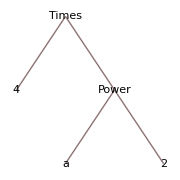

```mathematica
TreeForm[4*a^2]
```

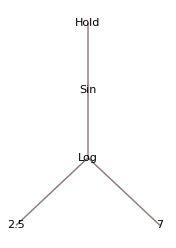

```mathematica
TreeForm[Hold[Sin[Log[2.5,7]]]]
```